# Linear Optimization Examples

## Jedi Battles

The Jedi Order is fighting the separatist armies led by Dooku. Dooku and two of his generals, Asajj Ventress and General Grievous, have attacked three outer colonies. The Jedi Order sends three Jedi to assist the outer colonies. Let p_ij be the odds of Jedi i beating Sith j:

```mathematica
p=({{0.4, 0.5, 0.5}, {0.6, 0.8, 0.6}, {0.7, 0.9, 0.6}});
```

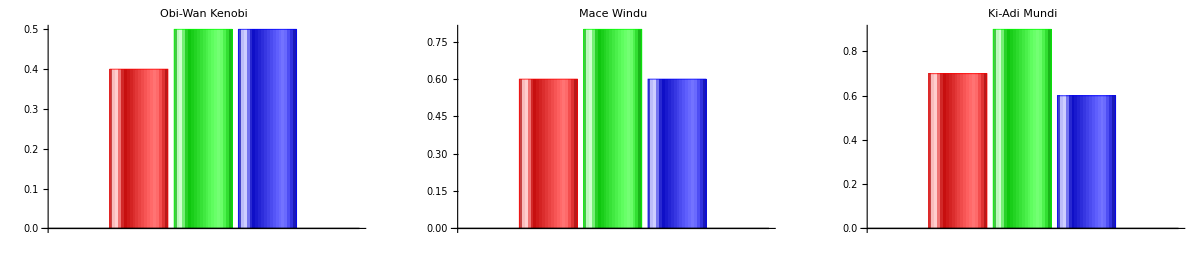

```mathematica
GraphicsRow[BarChart[p[[#]],]&/@Range[3]]
```

Let x be a matrix variable where x_ij is 1 if Jedi i battles Sith j, and 0 otherwise. The cost function is the expected number of defeats given by ∑_(i=1) ∑_(j=1) (1-p_ij)x_ij and constructed using Inactivepaclet:ref/Inactive[Timespaclet:ref/Times]:

```mathematica
defeats=Total[Inactive[Times][(1-p),x],2]
```

Total[{{0.6,0.5,0.5},{0.4,0.2,0.4},{0.3,0.1,0.4}}×x,2]

Since the outer colonies are far apart, each Jedi may only be assigned to one Sith, and vice versa. Also, since x_ij is 0 or 1, then x_ij≥0:

```mathematica
constraints={Total[x]-1==0,Total[x,{2}]-1==0,x\[VectorGreaterEqual]0};
```

```mathematica
rule=LinearOptimization[defeats,constraints,x∈Matrices[Dimensions[p]]]
```

{x→{{0.,0.,1.},{0.,1.,0.},{1.,0.,0.}}}

```mathematica
LinearOptimization[defeats,constraints,x∈Matrices[Dimensions[p]],"PrimalMinimumValue"]
```

1.